```mathematica
PacletInstall[ResourceObject["Wolfram/CodeEquivalenceUtilities"]]
```

OpenWrite::noopen: Cannot open C:\Users\peter\AppData\Roaming\Mathematica\Paclets\Repository\Wolfram__CodeEquivalenceUtilities-2.0.4\Documentation\English\SearchIndex\5\_0.cfs.

```mathematica
PacletFind["*CodeEqui*"]
```

{PacletObject[…]}

```mathematica
CodeEquivalentQ[RandomInteger/@Range[5],Array[RandomInteger,5]]
```

True

```mathematica
Needs["Wolfram`CodeEquivalenceUtilities`"]
```

```mathematica
MakeCanonicalForm[RandomInteger/@Range[10]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]

```mathematica
MakeCanonicalForm[Array[RandomInteger,10]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]

```mathematica
MakeCanonicalForm[RandomInteger/@Range[10]]===MakeCanonicalForm[Array[RandomInteger,10]]
```

True

```mathematica
{{-Graphics-, EquivalenceTestData}}[
First[Rest[Range/@Range[2^100]]],
Part[Table[Table[j,{j,i}],{i,2^100}],2]
]
```

<|Timing→<|SameQ→0.,EqualQ→0.,ToCanonicalForm1→1.973542,ToCanonicalForm2→3.148541|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧],2→HoldComplete[Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,1267650600228229401496703205376,1}]⟦2⟧]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

```mathematica
EquivalenceTestData[Array[RandomReal,1000],RandomReal/@Range[1000]]
```

<|Timing→<|SameQ→0.,EqualQ→0.,ToCanonicalForm1→1.060612,ToCanonicalForm2→2.35172|>,SameQ→False,EqualQ→False,CanonicalForms→<|1→HoldComplete[Table[ℛ[UniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,1000,1}]],2→HoldComplete[Table[ℛ[UniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,1000,1}]]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

```mathematica
MakeCanonicalForm[Array[RandomInteger,10],"Trace"->True]//Column
```

Array[RandomInteger,10]
Table[RandomInteger[Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1],{Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1,10}]
Table[RandomInteger[Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1],{Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1,1,10,1}]
Table[RandomInteger[S1∷ℤ],{S1∷ℤ,1,10,1}]
Table[RandomInteger[{0,S1∷ℤ}],{S1∷ℤ,1,10,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]

```mathematica
MakeCanonicalForm[RandomInteger/@Range[10],"Trace"->True]//Column
```

RandomInteger/@Range[10]
Map[RandomInteger,Range[10],{1}]
Map[RandomInteger,Table[Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1,{Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1,10}],{1}]
Table[RandomInteger[Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1],{Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1,10}]
Table[RandomInteger[Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1],{Wolfram`CodeEquivalenceUtilities`LocalSymbols`S1,1,10,1}]
Table[RandomInteger[S1∷ℤ],{S1∷ℤ,1,10,1}]
Table[RandomInteger[{0,S1∷ℤ}],{S1∷ℤ,1,10,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]

```mathematica
MakeCanonicalForm[RandomInteger/@Range[10]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1∷ℤ}]],{S1∷ℤ,1,10,1}]

```mathematica
FromCanonicalForm[MakeCanonicalForm[RandomInteger/@Range[10]]]
```

Table[RandomVariate[DiscreteUniformDistribution[{0,S1}]],{S1,1,10,1}]

```mathematica
ReleaseHold[FromCanonicalForm[MakeCanonicalForm[RandomInteger/@Range[10]]]]
```

{1,0,1,4,1,6,3,7,7,1}

```mathematica
expressions={
HoldForm[Table[i,{i,5},{j,i+2}]],
HoldForm[Array[Range,5,3]],
HoldForm[Table[ConstantArray[i,i+2],{i,5}]],
HoldForm[First[Rest[Range/@Range[10]]]],
HoldForm[Range/@Range[3,7]],
HoldForm[Part[Table[Table[j,{j,i}],{i,10}],2]]
};
```

```mathematica
Short[traces=Most@ToCanonicalForm[#,"Trace"->True]&/@expressions]
```

{{«1»},«4»,{«1»}}

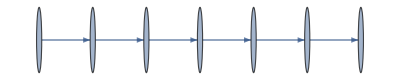
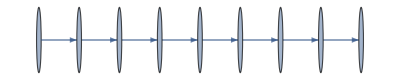
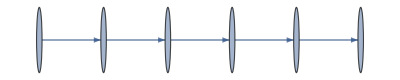
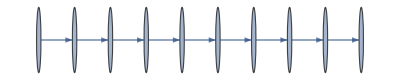
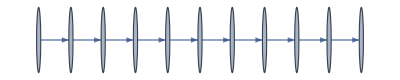
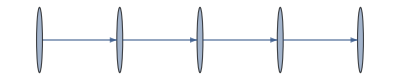

```mathematica
paths=Graph[DirectedEdge@@@Partition[#,2,1]]&/@traces
```

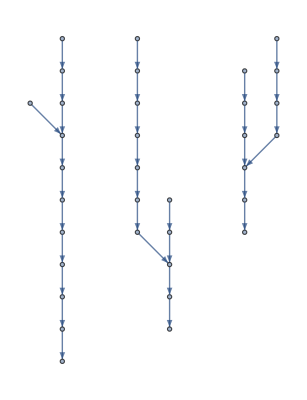

```mathematica
graph=Graph[GraphUnion@@paths,]
```

Equivalent expressions converge to the same connected component:

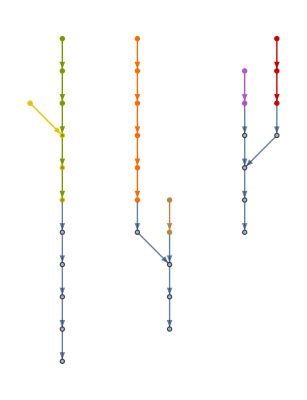

```mathematica
HighlightGraph[graph,paths]
```

```mathematica
grouped=GroupBy[expressions,ToCanonicalForm]
```

<|Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]→{Table[i,{i,5},{j,i+2}],Table[ConstantArray[i,i+2],{i,5}]},Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]→{Array[Range,5,3],Range/@Range[3,7]},Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧→{First[Rest[Range/@Range[10]]],Table[Table[j,{j,i}],{i,10}]⟦2⟧}|>

```mathematica
TableForm[KeyValueMap[Reverse@*List,grouped]]
```

Table[i,{i,5},{j,i+2}]
Table[ConstantArray[i,i+2],{i,5}] | Table[Table[S1∷ℤ,{S2∷ℤ,1,2+S1∷ℤ,1}],{S1∷ℤ,1,5,1}]
Array[Range,5,3]
Range/@Range[3,7] | Table[Table[S1∷ℤ,{S1∷ℤ,1,2+S2∷ℤ,1}],{S2∷ℤ,1,5,1}]
First[Rest[Range/@Range[10]]]
Table[Table[j,{j,i}],{i,10}]⟦2⟧ | Table[Table[S1∷ℤ,{S1∷ℤ,1,S2∷ℤ,1}],{S2∷ℤ,1,10,1}]⟦2⟧